```mathematica
BFAssumptions= {
r ∈ PositiveReals,
σ ∈ PositiveReals,
σ[s] ∈ PositiveReals,
δ∈ PositiveReals,
v[s]∈ PositiveReals,
Subscript[k, 1][s] ∈ Reals,
Subscript[k, 2][s]∈ Reals,
Subscript[k, 1]'[s]∈ Reals,
Subscript[k, 2]'[s]∈ Reals,
Subscript[k, 1]''[s]∈ Reals,
Subscript[k, 2]''[s]∈ Reals,
ψ[s]∈ Reals,
ψ'[s]∈ Reals,
γ[s]∈ Vectors[3, Reals],
t[s]∈ Vectors[3, Reals],
t'[s]∈ Vectors[3, Reals],
Subscript[n, 1][s]∈ Vectors[3, Reals],
Subscript[n, 1]'[s]∈ Vectors[3, Reals],
Subscript[n, 2]'[s]∈ Vectors[3, Reals],
Subscript[n, 2]'[s]∈ Vectors[3, Reals]
};

BFRules = {
γ'[s]->t[s]v[s],
t'[s] -> v[s](Subscript[k, 1][s]Subscript[n, 1][s]+Subscript[k, 2][s]Subscript[n, 2][s]),
Subscript[n, 1]'[s]->-Subscript[k, 1][s]t[s]v[s],
Subscript[n, 2]'[s]->-Subscript[k, 2][s]t[s]v[s],

t[s]⊗t[s] -> 1,
Subscript[n, 1][s]⊗Subscript[n, 1][s] -> 1,
Subscript[n, 2][s]⊗Subscript[n, 2][s] -> 1,

t[s]⊗Subscript[n, 1][s] -> 0,
Subscript[n, 1][s]⊗t[s] -> 0,
t[s]⊗Subscript[n, 2][s] -> 0,
Subscript[n, 2][s]⊗t[s] -> 0,
Subscript[n, 1][s]⊗Subscript[n, 2][s] -> 0,
Subscript[n, 2][s]⊗Subscript[n, 1][s] -> 0,

t[s]×t[s] -> 0,
Subscript[n, 1][s]×Subscript[n, 1][s] -> 0,
Subscript[n, 2][s]×Subscript[n, 2][s] -> 0,

t[s]×Subscript[n, 1][s] -> Subscript[n, 2][s],
Subscript[n, 1][s]×Subscript[n, 2][s] -> t[s],
Subscript[n, 2][s]×t[s] -> Subscript[n, 1][s],
Subscript[n, 1][s]×t[s] ->-Subscript[n, 2][s],
t[s]×Subscript[n, 2][s] -> -Subscript[n, 1][s],
Subscript[n, 2][s]×Subscript[n, 1][s] -> -t[s],
1/2 (1+δ^2+(-1+δ^2) Cos[2 φ])->(δ^2 Cos[φ]^2+Sin[φ]^2),
1/2  (1+δ^2-(-1+δ^2) Cos[2 φ])->(Cos[φ]^2+δ^2 Sin[φ]^2)
};

Rot[v_,k_,ψ_]:=v Cos[ψ]+(k×v)Sin[ψ]+k(k⊗v)(1-Cos[ψ])
BFGeometry[r_, s_,φ_] :=γ[s] - r σ Subscript[n, 1][s]Cos[φ]-r σ Subscript[n, 2][s]Sin[φ];

BFTSimplify[expr_]:=FullSimplify[TensorExpand[expr/.BFRules,Assumptions->BFAssumptions]/.BFRules,Trig->True]/.BFRules

Subscript[BFϵ, r][r_,s_,φ_]:=BFTSimplify[D[BFGeometry[r, s,φ],r]]
Subscript[BFϵ, s][r_,s_,φ_]:=BFTSimplify[D[BFGeometry[r, s,φ],s]]
Subscript[BFϵ, φ][r_,s_,φ_]:=BFTSimplify[D[BFGeometry[r, s,φ],φ]]
Subscript[BFg, rr][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, r][r,s,φ]⊗Subscript[BFϵ, r][r,s,φ]]
Subscript[BFg, ss][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, s][r,s,φ]⊗Subscript[BFϵ, s][r,s,φ]]
Subscript[BFg, φφ][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, φ][r,s,φ]⊗Subscript[BFϵ, φ][r,s,φ]]
Subscript[BFg, rs][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, r][r,s,φ]⊗Subscript[BFϵ, s][r,s,φ]]
Subscript[BFg, rφ][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, r][r,s,φ]⊗Subscript[BFϵ, φ][r,s,φ]]
Subscript[BFg, sφ][r_,s_,φ_]:=BFTSimplify[Subscript[BFϵ, s][r,s,φ]⊗Subscript[BFϵ, φ][r,s,φ]]
Subscript[BFg, ij][r_,s_,φ_]:={{Subscript[BFg, rr][r,s,φ],Subscript[BFg, rs][r,s,φ],Subscript[BFg, rφ][r,s,φ]},{Subscript[BFg, rs][r,s,φ],Subscript[BFg, ss][r,s,φ],Subscript[BFg, sφ][r,s,φ]},{Subscript[BFg, rφ][r,s,φ],Subscript[BFg, sφ][r,s,φ],Subscript[BFg, φφ][r,s,φ]}};
BFsqg[r_, s_, φ_]:=BFTSimplify[Sqrt[Det[Subscript[BFg, ij][r,s,φ]]]]//.Sqrt[x_^2 y_]:>x Sqrt[y]/.Sqrt[x_^4]:>x^2

Subscript[BFh, r][r_, s_, φ_] := BFTSimplify[Sqrt[Subscript[BFg, rr][r,s,φ]]]
Subscript[BFh, s][r_, s_, φ_] := BFTSimplify[Sqrt[Subscript[BFg, ss][r,s,φ]]]
Subscript[BFh, φ][r_, s_, φ_] := BFTSimplify[Sqrt[Subscript[BFg, φφ][r,s,φ]]]

Subscript[BFB, r][r_,s_,φ_]:=0
Subscript[BFB, s][r_,s_,φ_]:= -1/v[s](Subscript[μ, 0] σ Sqrt[1-r^2 σ^2 (Subscript[k, 1][s])^2-r^2 σ^2 (Subscript[k, 2][s])^2])/(1+r σ  Cos[φ] Subscript[k, 1][s]+r σ  Sin[φ] Subscript[k, 2][s])^2∑_(n=0)^Subscript[n, m] α[n]LegendreP[n, 2r-1] 
Subscript[BFB, φ][r_,s_,φ_]:=(-Subscript[μ, 0])/(1+r σ  Cos[φ] Subscript[k, 1][s]+r σ  Sin[φ] Subscript[k, 2][s])(∑_(m=0)^Subscript[m, m] β[m]LegendreP[m, 2r-1])-(r σ^2 Subscript[μ, 0] ((Sin[φ]+r σ Subscript[k, 2][s]) Subscript[k, 1]'[s]-(Cos[φ]+r σ Subscript[k, 1][s]) Subscript[k, 2]'[s]))/(v[s] (1+r σ Cos[φ] Subscript[k, 1][s]+r σ Sin[φ] Subscript[k, 2][s])^2 √(1-r^2 σ^2 (Subscript[k, 1][s])^2-r^2 σ^2 (Subscript[k, 2][s])^2))∑_(n=0)^Subscript[n, m] α[n]LegendreP[n, 2r-1] 


Subscript[BFB, D][r_,s_,φ_]:=D[BFsqg[r,s,φ]Subscript[BFB, s][r,s,φ],s]+D[BFsqg[r,s,φ]Subscript[BFB, φ][r,s,φ],φ]
Subscript[BFJ, r][r_,s_,φ_]:= (D[Subscript[BFg, sφ][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, φφ][r,s,φ]Subscript[BFB, φ][r,s,φ],s] - D[Subscript[BFg, ss][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, sφ][r,s,φ]Subscript[BFB, φ][r,s,φ],φ]) /BFsqg[r, s, φ] / Subscript[μ, 0]
Subscript[BFJ, s][r_,s_,φ_]:= (D[Subscript[BFg, rs][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, rφ][r,s,φ]Subscript[BFB, φ][r,s,φ],φ] - D[Subscript[BFg, sφ][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, φφ][r,s,φ]Subscript[BFB, φ][r,s,φ],r]) /BFsqg[r, s, φ] / Subscript[μ, 0]
Subscript[BFJ, φ][r_,s_,φ_]:= (D[Subscript[BFg, ss][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, sφ][r,s,φ]Subscript[BFB, φ][r,s,φ],r] - D[Subscript[BFg, rs][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFg, rφ][r,s,φ]Subscript[BFB, φ][r,s,φ],s]) /BFsqg[r, s, φ] / Subscript[μ, 0]

Subscript[BFF, r][r_,s_,φ_]:=Simplify[Inverse[Subscript[BFg, ij][r,s,φ]]][[1]][[1]]BFsqg[r, s, φ](Subscript[BFJ, s][r,s,φ]Subscript[BFB, φ][r,s,φ]-Subscript[BFJ, φ][r,s,φ]Subscript[BFB, s][r,s,φ])
Subscript[BFF, s][r_,s_,φ_]:=Simplify[Inverse[Subscript[BFg, ij][r,s,φ]]][[2]][[2]]BFsqg[r, s, φ](-Subscript[BFJ, r][r,s,φ]Subscript[BFB, φ][r,s,φ])+Simplify[Inverse[Subscript[BFg, ij][r,s,φ]]][[2]][[3]]BFsqg[r, s, φ](Subscript[BFJ, r][r,s,φ]Subscript[BFB, s][r,s,φ])
Subscript[BFF, φ][r_,s_,φ_]:=Simplify[Inverse[Subscript[BFg, ij][r,s,φ]]][[3]][[3]]BFsqg[r, s, φ](Subscript[BFJ, r][r,s,φ]Subscript[BFB, s][r,s,φ])+Simplify[Inverse[Subscript[BFg, ij][r,s,φ]]][[2]][[3]]BFsqg[r, s, φ](-Subscript[BFJ, r][r,s,φ]Subscript[BFB, s][r,s,φ])

Bv[r_,s_,φ_]:= Subscript[BFϵ, s][r,s,φ]Subscript[BFB, s][r,s,φ]+Subscript[BFϵ, φ][r,s,φ]Subscript[BFB, φ][r,s,φ]

Jv[r_,s_,φ_]:= Subscript[BFϵ, r][r,s,φ]Subscript[BFJ, r][r,s,φ]+Subscript[BFϵ, s][r,s,φ]Subscript[BFJ, s][r,s,φ]+Subscript[BFϵ, φ][r,s,φ]Subscript[BFJ, φ][r,s,φ]
Fv[r_,s_,φ_]:= Subscript[BFϵ, r][r,s,φ]Subscript[BFF, r][r,s,φ]+Subscript[BFϵ, s][r,s,φ]Subscript[BFF, s][r,s,φ]+Subscript[BFϵ, φ][r,s,φ]Subscript[BFF, φ][r,s,φ]
```

```mathematica
Subscript[BFB, D][r,s,φ]//Simplify
```

0

```mathematica
LPCoeff[n_] := Integrate[Subscript[B, 0]/(1+Subscript[ζ, 0]^2 r^2) LegendreP[n, 2r-1](2n+1), {r, 0, 1}, Assumptions->{Subscript[ζ, 0]∈ Reals}] // Normal
ConfigGH = {
β[m_]:>-Subscript[ζ, 0] α[m],
Subscript[n, m]->12,Subscript[m, m]->12,
α[0] -> -LPCoeff[0],
α[1] -> -LPCoeff[1],
α[2] -> -LPCoeff[2],
α[3] -> -LPCoeff[3],
α[4] -> -LPCoeff[4],
α[5] -> -LPCoeff[5],
α[6] -> -LPCoeff[6],
α[7] -> -LPCoeff[7],
α[8] -> -LPCoeff[8],
α[9] -> -LPCoeff[9],
α[10] -> -LPCoeff[10],
α[11] -> -LPCoeff[11]
};
ConfigGH=Join[ConfigGH,Solve[∑_(n=0)^Subscript[n, m] (-1)^(1+n) (n+n^2) α[n]==0 //. ConfigGH,α[12]] // Flatten];
ConfigGeneral = {
Subscript[μ, 0] -> 1,
Subscript[B, 0]->15 / σ,
Subscript[ζ, 0] ->1,
σ->.1,
Subscript[r, 0] -> 1
};
Pγ={
{-1,0,0},
{-.8,0.1,0.1},
{-.6,0.3,0.2},
{-.4,0.35,0.3},
{-.2,0.25,0.4},
{0,0.1,.5},
{0.2,-0.05,0.4},
{0.4,-0.05,0.3},
{0.6,-0.05,0.2},
{0.8,-0.075,.1},
{1.0,0,0}
}//Transpose;

Eγ[s_]:={
Interpolation[{Range[0,1,1/((Pγ[[1]]//Length)-1)],Pγ[[1]]}//Transpose,InterpolationOrder->4,Method->"Spline"][s],
Interpolation[{Range[0,1,1/((Pγ[[1]]//Length)-1)],Pγ[[2]]}//Transpose,InterpolationOrder->4,Method->"Spline"][s],
Interpolation[{Range[0,1,1/((Pγ[[1]]//Length)-1)],Pγ[[3]]}//Transpose,InterpolationOrder->4,Method->"Spline"][s]
};

Show[{
ParametricPlot3D[Eγ[s],{s,0,1},PlotStyle->{Blue,Dashed}],
Graphics3D[{Black,PointSize[Large],Point[Pγ//Transpose]}],
Graphics3D[{Green,PointSize[Large],Point[Eγ[0]]}],Graphics3D[{Red,PointSize[Large],Point[Eγ[1]]}]
},AxesLabel->{"X","Y","Z"},Boxed->False,Axes->None]
```

-Graphics3D-

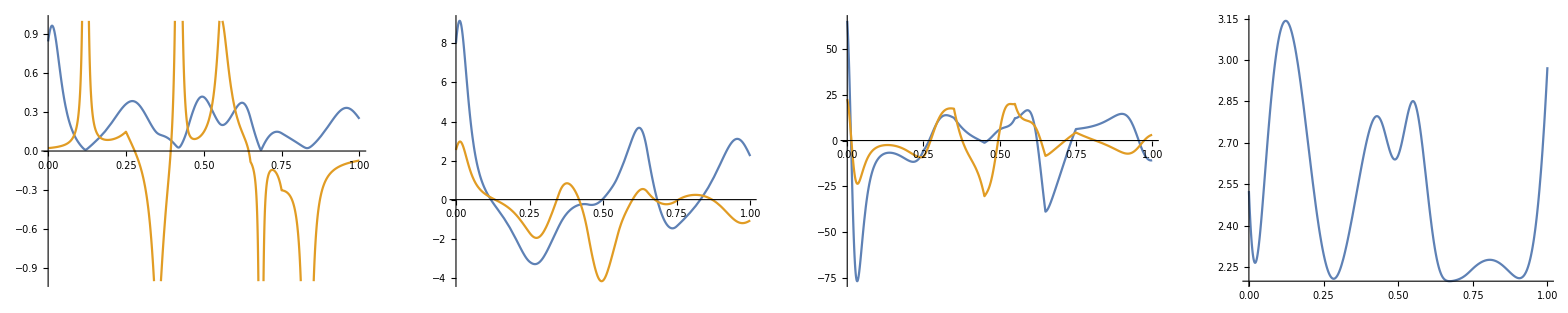

```mathematica
Er[s_] := Eγ[s] - r σ En[s]Cos[φ]-r σ   Eb[s]Sin[φ];
ErQ[s_] := Eγ[s] - r σ Subscript[En, 1][s]Cos[φ]-r σ   Subscript[En, 2][s]Sin[φ];
EDγ[s_] := Norm[D[Eγ[s] // ComplexExpand,s]]
Et[s_] :=D[Eγ[s] // ComplexExpand,s]//Normalize
En[s_] := D[Et[s] // ComplexExpand,s]//Normalize
Eb[s_] := Et[s]×En[s]// Normalize
Er[s_] := Eγ[s] - r σ En[s] Cos[φ]-r σ  Eb[s]Sin[φ];

Eκ[s_] :=Sqrt[ (Cross[Eγ'[s], Eγ''[s]].Cross[Eγ'[s], Eγ''[s]])/(Eγ'[s].Eγ'[s])^3]
Eτ[s_] :=(Eγ'[s].Cross[Eγ''[s], Derivative[3][Eγ][s]])/Norm[Eγ'[s]×Eγ''[s]]^2

BFMAT:= EDγ[s]{
{0,Subscript[k, 1][s],Subscript[k, 2][s]},
{-Subscript[k, 2][s],0,0},
{-Subscript[k, 2][s],0,0}
};

Subscript[IEn, 1]=En[s]/.s->Subscript[s, 0];
Subscript[IEn, 2]=Eb[s]/.s->Subscript[s, 0];

Subscript[En, 1][s_]:={Subscript[Enx, 1][s],Subscript[Eny, 1][s],Subscript[Enz, 1][s]}
Subscript[En, 2][s_]:=Et[s]×Subscript[En, 1][s]

BFEqs[s0_]:=Join[
D[Subscript[En, 1][s]//ComplexExpand,s]== -Subscript[k, 1][s]EDγ[s]Et[s]//Thread,
{
D[Subscript[k, 1][s],s]==(Dot[Subscript[En, 1][s],D[Et[s]//ComplexExpand,{s,2}]]-Subscript[k, 1][s]D[EDγ[s]//ComplexExpand,s])/EDγ[s],
D[Subscript[k, 2][s],s]==(Dot[Subscript[En, 2][s],D[Et[s]//ComplexExpand,{s,2}]]-Subscript[k, 2][s]D[EDγ[s]//ComplexExpand,s])/EDγ[s]
},
Subscript[En, 1][s]==En[s]/.s->s0//Thread,
{Subscript[k, 1][s]==Eκ[s],Subscript[k, 2][s]==0}/.s->s0
];

RPAFEqsSol=NDSolve[BFEqs[0.6],{Subscript[Enx, 1][s],Subscript[Eny, 1][s],Subscript[Enz, 1][s],Subscript[k, 1][s],Subscript[k, 2][s]},{s,0,1}]//Flatten;
GraphicsRow[{Plot[{Eκ[s]σ,Eτ[s]σ}//.ConfigGeneral/.RPAFEqsSol//Evaluate,{s,0.0,1},PlotRange->{-1,1}],
Plot[{Subscript[k, 1][s],Subscript[k, 2][s]}/.RPAFEqsSol//Evaluate,{s,0.0,1},PlotRange->All],
Plot[{D[Subscript[k, 1][s]/.RPAFEqsSol,s],D[Subscript[k, 2][s]/.RPAFEqsSol,s]}/EDγ[s]/.RPAFEqsSol//Evaluate,{s,0.0,1},PlotRange->All],
Plot[{EDγ[s]/.RPAFEqsSol}//Evaluate,{s,0.0,1},PlotRange->All]}]

RPAFEqsSols1=NDSolve[BFEqs[0.1],{Subscript[Enx, 1][s],Subscript[Eny, 1][s],Subscript[Enz, 1][s],Subscript[k, 1][s],Subscript[k, 2][s]},{s,0,1}]//Flatten;
RPAFEqsSols2=NDSolve[BFEqs[0.45],{Subscript[Enx, 1][s],Subscript[Eny, 1][s],Subscript[Enz, 1][s],Subscript[k, 1][s],Subscript[k, 2][s]},{s,0,1}]//Flatten;
RPAFEqsSols3=NDSolve[BFEqs[0.65],{Subscript[Enx, 1][s],Subscript[Eny, 1][s],Subscript[Enz, 1][s],Subscript[k, 1][s],Subscript[k, 2][s]},{s,0,1}]//Flatten;
```

```mathematica
Subscript[t, 0]=0.45;
Subscript[t, 1]=0.65;

Show[
{
ParametricPlot3D[Eγ[s] // Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, PlotStyle->{Black, Thickness[.005]}],
ParametricPlot3D[ErQ[s]/.σ->.1/.r->1/.RPAFEqsSol/. r->1// Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, {φ, 0,2 Pi}, PlotStyle->{Opacity[0.1],Black}, Mesh-> {10, 4}],
Graphics3D[{Arrowheads[.015],Thickness[.005], Black,Dashed,{Arrow[{Eγ[s],Eγ[s]+1σ En[s]}/.s->0.55/.σ->.1/.r->1/.RPAFEqsSol]}}],
Graphics3D[{Arrowheads[.015],Thickness[.005], Black,Dashed,{Arrow[{Eγ[s],Eγ[s]+1σ Eb[s]}/.s->0.55/.σ->.1/.r->1/.RPAFEqsSol]}}],
Graphics3D[{Arrowheads[.025],Thickness[.005], Black,{Arrow[{Eγ[s],Eγ[s]+1σ Et[s]}/.RPAFEqsSol/.s->0.55 /.σ->.1/.r->1]}}],
Graphics3D[{Arrowheads[.025],Thickness[.005], Black,{Arrow[{Eγ[s],Eγ[s]+1σ Subscript[En, 1][s]}/.RPAFEqsSol/.s->0.55/.σ->.1/.r->1]}}],
Graphics3D[{Arrowheads[.025],Thickness[.005], Black,{Arrow[{Eγ[s],Eγ[s]+1σ Subscript[En, 2][s]}/.RPAFEqsSol/.s->0.55/.σ->.1/.r->1]}}],
ParametricPlot3D[ErQ[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->Pi// Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, PlotStyle->{Opacity[1],Magenta,Thickness[0.004]}],
ParametricPlot3D[Er[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->Pi// Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, PlotStyle->{Opacity[0.5],Magenta ,Dashed,,Thickness[0.004]}],
ParametricPlot3D[ErQ[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->-Pi/2// Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, PlotStyle->{Opacity[1],Red,Thickness[0.004]}],
ParametricPlot3D[Er[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->-Pi/2// Evaluate, {s,Subscript[t, 0],Subscript[t, 1]}, PlotStyle->{Opacity[0.5],Red ,Dashed,,Thickness[0.004]}],
Graphics3D[{Black,Text[Style["t",24],{Eγ[s]+1.15σ Et[s]+0.1σ Subscript[En, 2][s]}/.RPAFEqsSol/. s -> 0.55/. ConfigGeneral/. r -> 1.25]}],
Graphics3D[{Black,Text[Style["n_1",24],{Eγ[s]+1.15σ Subscript[En, 1][s]-0.1σ Subscript[En, 2][s]}/.RPAFEqsSol/.  s -> 0.55 /. ConfigGeneral/. r -> 0.25]}],
Graphics3D[{Black,Text[Style["n_2",24],{Eγ[s]+1.15σ Subscript[En, 2][s]-0.1σ Subscript[En, 1][s]}/.RPAFEqsSol/.  s -> 0.55 /. ConfigGeneral /. r -> 0.25]}],
Graphics3D[{Black,Text[Style["φ=π",18,Magenta],ErQ[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->Pi/.s->Subscript[t, 0]-0.02]}],
Graphics3D[{Black,Text[Style["φ=(3  π)/2",18,Red],ErQ[s]/.σ->.1/.r->1/.RPAFEqsSol/.φ->3Pi/2/.s->Subscript[t, 0]-0.02]}]
},
PlotRange->All, Boxed->False, Axes->False
]
```

-Graphics3D-

```mathematica
smax=1;
p[t_] := {p1[t],p2[t],p3[t]}
RCoords={r->p1[t],s->p2[t],φ->p3[t]};
ConfigE = {γ[s] ->Eγ[s], t[s]->Et[s],Subscript[n, 1][s]->Subscript[En, 1][s],Subscript[n, 2][s]->Subscript[En, 2][s],v[s]->EDγ[s],D[Subscript[k, 1][s],s]->D[Subscript[k, 1][s]/.RPAFEqsSol//ComplexExpand,s],D[Subscript[k, 2][s],s]->D[Subscript[k, 2][s]/.RPAFEqsSol//ComplexExpand,s]};
eqsInitial:=Thread[p[0]=={.9,.1,3Pi/4}];
If[False,
eqsB=Thread[D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords// ComplexExpand,t]==Bv[r,s,φ]/ Norm[Bv[r,s,φ]]//.ConfigE/.RPAFEqsSol//.ConfigGH//.ConfigGeneral/.RCoords];
eqsSolve=NDSolve[{eqsB,eqsInitial,WhenEvent[p2[t] >= .9,smax=t;"StopIntegration"]},{p1,p2,p3},{t,0,Infinity},Method->{"EquationSimplification"->"Residual"}] // Flatten;
]
smaxNaive=1;
eqsBNaive=Thread[D[BFGeometry[r,s,φ]/.{D[Subscript[k, 1][s],s]->0,D[Subscript[k, 2][s],s]->0}//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords// ComplexExpand,t]==Bv[r,s,φ]/ Norm[Bv[r,s,φ]]/.{D[Subscript[k, 1][s],s]->0,D[Subscript[k, 2][s],s]->0}//.ConfigE/.RPAFEqsSol//.ConfigGH//.ConfigGeneral/.RCoords];
eqsSolveNaive=NDSolve[{eqsBNaive,eqsInitial,WhenEvent[p2[t] >=.9,smaxNaive=t;"StopIntegration"]},{p1,p2,p3},{t,0,Infinity},Method->{"EquationSimplification"->"Residual"}] // Flatten;
If[True,
eqsBApprox=Thread[D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords// ComplexExpand,t]==Bv[r,s,φ]/ Norm[Bv[r,s,φ]]//.ConfigE/.RPAFEqsSol//.ConfigGH//.ConfigGeneral/.RCoords];
eqsSolveApprox=NDSolve[{eqsBApprox,eqsInitial,WhenEvent[p2[t] >= .9,smax=t;"StopIntegration"]},{p1,p2,p3},{t,0,Infinity},Method->{"EquationSimplification"->"Residual"}] // Flatten;
]
```

```mathematica
eqsSolveApprox
```

{p1→InterpolatingFunction[…],p2→InterpolatingFunction[…],p3→InterpolatingFunction[…]}

```mathematica
pa1 =ErQ[s]/.ConfigE/.RPAFEqsSol/. ConfigGeneral /. r->1/.s->0.52/.φ->Pi/4+Pi;
pa2 =ErQ[s]/.ConfigE/.RPAFEqsSol/. ConfigGeneral /. r->0/.s->0.5/.φ->Pi/4;
pa[t_]:=pa1+(pa2-pa1)t

pb1 =ErQ[s]/.ConfigE/.RPAFEqsSol/. ConfigGeneral /. r->1/.s->0.35/.φ->Pi/4+Pi;
pb2 =ErQ[s]/.ConfigE/.RPAFEqsSol/. ConfigGeneral /. r->.1/.s->0.5/.φ->Pi/4+Pi/10;
pb[t_]:=pb1+(pb2-pb1)t
X0={-0.25,-0.15,-0.25};
XL=0.25;
XV={X0,X0+XL{1,0,0}};
YV={X0,X0+XL{0,1,0}};
ZV={X0,X0+XL{0,0,1}};

vpv=Options[Plot3D,ViewPoint][[1,2]];
Show[{
ParametricPlot3D[Eγ[s] // Evaluate, {s,0,1}, PlotStyle->{Blue, Thickness[.0015]}],
ParametricPlot3D[ErQ[s]//.ConfigGeneral/.r->1/.RPAFEqsSol// Evaluate, {s,0,1},{φ,0,2Pi}, PlotStyle->{Black, Thickness[.00025],Opacity[0.005]},Mesh->{50,10}],
ParametricPlot3D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords/. eqsSolveNaive // Evaluate,{t,0,smaxNaive}, PlotStyle->{Red,Dashed,Thickness[.004]}],
ParametricPlot3D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords/. eqsSolveApprox // Evaluate,{t,0,smax}, PlotStyle->{Red,Thickness[.003]}],
Graphics3D[{Black,PointSize[Large],Point[Pγ//Transpose]}],
Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.1]]}],Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.45]]}],Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.65]]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{pa[t]/.t->-2,pa[t]/.t->4}]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{pb[t]/.t->-1.5,pb[t]/.t->3}]}],
Graphics3D[Text[Style["x",16],1.15*(XV[[2]]-X0)+X0]],
Graphics3D[Text[Style["y",16],1.25*(YV[[2]]-X0)+X0]],
Graphics3D[Text[Style["z",16],1.25*(ZV[[2]]-X0)+X0]],
Graphics3D[{Arrowheads[.025],Thickness[.0035],Arrow[XV]}],
Graphics3D[{Arrowheads[.025],Thickness[.0035],Arrow[YV]}],
Graphics3D[{Arrowheads[.025],Thickness[.0035],Arrow[ZV]}],
Graphics3D[Text[Style["t_1",18],pa[-1.75]+{-.1,0,.05}]],
Graphics3D[Text[Style["t_2",18],pb[-2.25]+{.12,0,0}]]
},PlotRange->All,Boxed->False,Axes->False,ImageSize->650,ViewPoint->{2.0791161083564726,-2.3499417431865415,1.2669056837831438},AxesLabel->{"x","y","z"},AxesStyle->Medium,TicksStyle->Medium,LabelStyle->Black,
Epilog->{Text[Style["a)",18],Scaled[{0.1,0.75}]]}]
Show[{
ParametricPlot3D[Eγ[s] // Evaluate, {s,0,1}, PlotStyle->{Blue, Thickness[.0015]}],
ParametricPlot3D[ErQ[s]//.ConfigGeneral/.r->1/.RPAFEqsSol// Evaluate, {s,0,1},{φ,0,2Pi}, PlotStyle->{Black, Thickness[.00025],Opacity[0.005]},Mesh->{50,10}],
ParametricPlot3D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords/. eqsSolveNaive // Evaluate,{t,0,smaxNaive-0.1}, PlotStyle->{Red,Dashed,Thickness[.004]}],
ParametricPlot3D[BFGeometry[r,s,φ]//.ConfigE/.RPAFEqsSol//.ConfigGeneral/.RCoords/. eqsSolveApprox // Evaluate,{t,0,smax-0.1}, PlotStyle->{Red,Thickness[.003]}],
Graphics3D[{Black,PointSize[Large],Point[Pγ//Transpose]}],
Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.1]]}],Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.45]]}],Graphics3D[{Orange,PointSize[Large],Point[Eγ[0.65]]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{pa[t]/.t->-2,pa[t]/.t->4}]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{pb[t]/.t->-0.5,pb[t]/.t->2.5}]}],
Graphics3D[{Arrowheads[.025],Thickness[.0035],Arrow[XV]}],
Graphics3D[{Arrowheads[.025],Thickness[.0035],Arrow[YV]}],
Graphics3D[Text[Style["x",16],1.15*(XV[[2]]-X0)+X0]],
Graphics3D[Text[Style["y",16],1.25*(YV[[2]]-X0)+X0]],
Graphics3D[Text[Style["t_1",18],pa[-2.25]+{-.1,.05,.05}]],
Graphics3D[Text[Style["t_2",18],pb[-0.65]+{-.01,0,0}]]
},PlotRange->All,Boxed->False,Axes->False,ImageSize->650,ViewPoint->{0,-1,3},AxesLabel->{"x","y","z"},AxesStyle->Medium,TicksStyle->Medium,LabelStyle->Black,
Epilog->{Text[Style["b)",18],Scaled[{0.1,0.95}]]}]
```

-Graphics3D-

-Graphics3D-

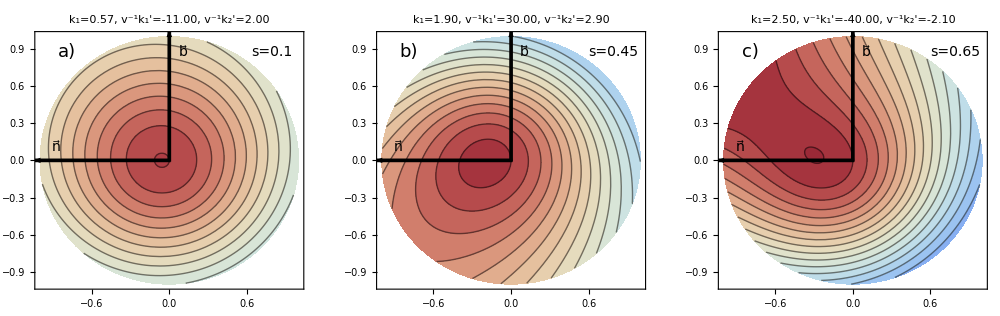

```mathematica
ConfigSol[sol_]:={γ[s]->Eγ[s],t[s]->Et[s],Subscript[n, 1][s]->Subscript[En, 1][s],Subscript[n, 2][s]->Subscript[En, 2][s],v[s]->EDγ[s],D[v[s],s]->D[EDγ[s]//ComplexExpand,s],D[Subscript[k, 1][s], s]->D[ComplexExpand[Subscript[k, 1][s]/.sol], s],D[Subscript[k, 2][s], s]->D[ComplexExpand[Subscript[k, 2][s]/.sol], s],D[Subscript[k, 1][s],{s,2}]->D[Subscript[k, 1][s]/.sol,{s,2}],D[Subscript[k, 2][s],{s,2}]->D[Subscript[k, 2][s]/.sol,{s,2}]}
StringFunc[t_,sol_]:="k_1="<>ToString[NumberForm[Subscript[k, 1][s]/.sol/.s->t//N,{2,2}]]<>", v^-1k_1'="<>ToString[NumberForm[D[Subscript[k, 1][s]/.sol//ComplexExpand,s]/EDγ[s]/.sol/.s->t//Evaluate//N,{2,2}]]<> ", v^-1k_2'="<>ToString[NumberForm[D[Subscript[k, 2][s]/.sol//ComplexExpand,s]/EDγ[s]/.sol/.s->t//Evaluate//N,{2,2}]]
StringFuncF[t_,sol_]:="k_1="<>ToString[NumberForm[Subscript[k, 1][s]/.sol/.s->t//N,{2,2}]]<>", v^-1k_1'="<>ToString[NumberForm[D[Subscript[k, 1][s]/.sol//ComplexExpand,s]/EDγ[s]/.sol/.s->t//Evaluate//N,{2,2}]]<>", k_2="<>ToString[NumberForm[Subscript[k, 2][s]/.sol/.s->t//N,{2,2}]]<>", v^-1k_2'="<>ToString[NumberForm[D[Subscript[k, 2][s]/.sol//ComplexExpand,s]/EDγ[s]/.sol/.s->t//Evaluate//N,{2,2}]]
BT[sol_,pv_]:=Norm[Bv[r,s,φ]]//.ConfigGH//.ConfigGeneral//.ConfigSol[sol]/.sol/.RCoords/.p1[t]->√(x^2+y^2)/.p3[t]->Arg[x+ⅈ y]/.p2[t]->pv

IMS=250;
FSA=12;
FSB=14;

CSB=GraphicsRow[{
Show[{ContourPlot[
BT[RPAFEqsSols1,0.1]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->StringFunc[0.1,RPAFEqsSols1], ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["a)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.1",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BT[RPAFEqsSols2,0.45]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->StringFunc[0.45,RPAFEqsSols2], ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["b)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.45",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BT[RPAFEqsSols3,0.65]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->StringFunc[0.65,RPAFEqsSols3], ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["c)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.65",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
BarLegend[{"ThermometerColors",{5,16}},Range[5, 16,1],LegendMargins->0,LegendLabel->"B [nT]",LabelStyle->{FontSize->FSB,FontColor->Black},LegendMarkerSize->IMS*0.9]
},ImageSize->4*IMS,Alignment->Left
]
```

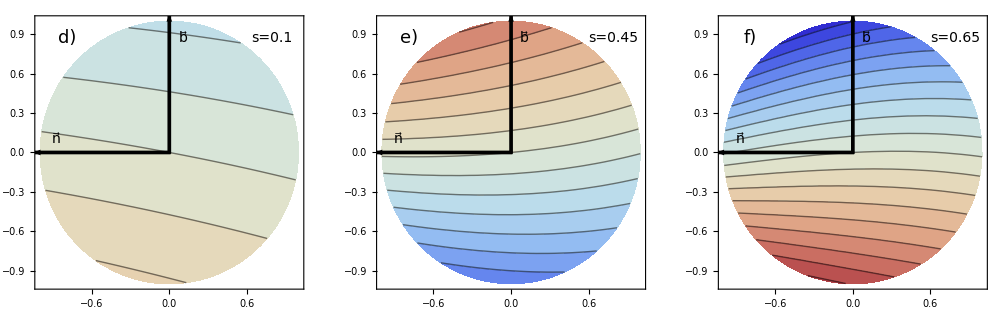

```mathematica
BTA[sol_,pv_]:=Subscript[BFh, φ][r,s,φ]Subscript[BFB, φ][r,s,φ]/(r Subscript[BFh, s][r,s,φ]Subscript[BFB, s][r,s,φ])//.ConfigGH//.ConfigGeneral//.ConfigSol[sol]/.sol/.RCoords/.p1[t]->√(x^2+y^2)/.p3[t]->Arg[x+ⅈ y]/.p2[t]->pv
TMAX=-0.5;
TMIN=-1.5;
TRES=0.05;
CSB=GraphicsRow[{
Show[{ContourPlot[
BTA[RPAFEqsSols1,0.1]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[TMIN, TMAX,TRES], MaxRecursion->1, ColorFunction->ColorData[{"ThermometerColors",{TMIN, TMAX}}],ColorFunctionScaling->False, ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["d)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.1",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BTA[RPAFEqsSols2,0.45]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[TMIN, TMAX,TRES], MaxRecursion->1, ColorFunction->ColorData[{"ThermometerColors",{TMIN, TMAX}}],ColorFunctionScaling->False, ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["e)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.45",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BTA[RPAFEqsSols3,0.65]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[TMIN, TMAX,TRES], MaxRecursion->1, ColorFunction->ColorData[{"ThermometerColors",{TMIN, TMAX}}],ColorFunctionScaling->False, ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["f)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.65",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
BarLegend[{"ThermometerColors",{TMIN, TMAX}},Range[TMIN, TMAX,0.05],LegendMargins->0,LegendLabel->"Q",LabelStyle->{FontSize->FSB,FontColor->Black},LegendMarkerSize->IMS*0.9]
},ImageSize->4*IMS,Alignment->Left
]
```

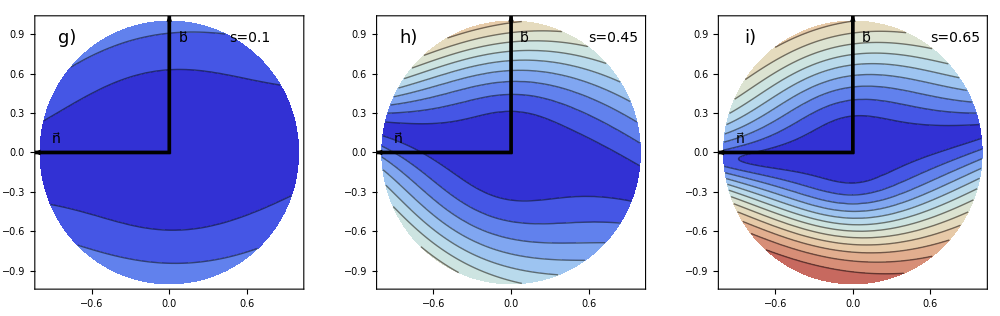

```mathematica
BvE[sol_,pv_]:=Bv[r,s,φ]//.ConfigGH//.ConfigGeneral//.ConfigSol[sol]/.sol/.s->pv
JvE[sol_,pv_]:=Jv[r,s,φ]//.ConfigGH//.ConfigGeneral//.ConfigSol[sol]/.sol/.s->pv
BJA[sol_,pv_]:=180/Pi ArcSin[Norm[JvE[sol,pv]×BvE[sol,pv]]/(Norm[BvE[sol,pv]]Norm[JvE[sol,pv]])]/.RCoords/.p1[t]->√(x^2+y^2)/.p3[t]->Arg[x+ⅈ y]/.p2[t]->pv
MAXANGLE=90;
MAXANGLERES=6;
CSJB=GraphicsRow[{
Show[{ContourPlot[
BJA[RPAFEqsSols1,0.1]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, MAXANGLE,MAXANGLERES], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, MAXANGLE}}],ColorFunctionScaling->False,ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["g)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.1",FSB],Scaled[{0.8,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BJA[RPAFEqsSols2,0.45]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, MAXANGLE,MAXANGLERES], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, MAXANGLE}}],ColorFunctionScaling->False,ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["h)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.45",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
Show[{ContourPlot[
BJA[RPAFEqsSols3,0.65]//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, MAXANGLE,MAXANGLERES], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, MAXANGLE}}],ColorFunctionScaling->False,ImageSize->{IMS,IMS},ContourLabels->None,LabelStyle->{FontSize->FSA,FontColor->Black},
Epilog->{Text[Style["i)",18],Scaled[{0.12,0.92}]],Text[Style["s=0.65",FSB],Scaled[{0.88,0.92}]],Text[Style[OverVector ["n"],FSB],Scaled[{0.08,0.55}]],Text[Style[OverVector ["b"],FSB],Scaled[{0.55,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
],Graphics[{AbsoluteThickness[2.66],{Arrowheads[.05],Arrow[{{0.01,0},{-1.05,0}}]},{Arrowheads[.05],Arrow[{{0.00,-0.01},{0,1.05}}]}}]}],
BarLegend[{"ThermometerColors",{0,MAXANGLE}},Range[0, MAXANGLE,MAXANGLERES],LegendMargins->0,LegendLabel->"α [deg]",LabelStyle->{FontSize->FSB,FontColor->Black},LegendMarkerSize->IMS*0.9]
},ImageSize->4*IMS,Alignment->Left
]
```

```mathematica
Bfs[repr_]:=Bv[r,s,φ]//.ConfigE//.RPAFEqsSol//.ConfigGH//.ConfigGeneral/.repr

coordsa = {};
tparamsa={};
trangea=Range[-0.2,2.5,0.01];
For[i=1,i<Length[trangea],i++,
{
σF=σ/.ConfigGeneral;
sol=NMinimize[{Norm[(Eγ[s]-pa[trangea[[i]]])]//Evaluate,s∈PositiveReals} ,s,Method->"DifferentialEvolution"];
solr={r->sol[[1]]/σF};
sols=sol[[2]];
If[sol[[1]]/σF<=1,
solp={φ->ArcTan[-(Subscript[En, 1][s]//.ConfigE//.RPAFEqsSol/.ConfigGeneral/.sols).(pa[trangea[[i]]]-Eγ[s/.sols]),-(Subscript[En, 2][s]//.ConfigE//.RPAFEqsSol/.ConfigGeneral/.sols).(pa[trangea[[i]]]-Eγ[s/.sols])]};
coordsa=AppendTo[coordsa,Join[solr,sols,solp]]; 
tparamsa=AppendTo[tparamsa,trangea[[i]]]
];
}
]

coordsb = {};
tparamsb={};
trangeb=Range[-0.2,2,0.01];
For[i=1,i<Length[trangeb],i++,
{
σF=σ/.ConfigGeneral;
sol=NMinimize[{Norm[(Eγ[s]-pb[trangea[[i]]])]//Evaluate,s∈PositiveReals} ,s,Method->"DifferentialEvolution"];
solr={r->sol[[1]]/σF};
sols=sol[[2]];
If[sol[[1]]/σF<=1,
solp={φ->ArcTan[-(Subscript[En, 1][s]//.ConfigE//.RPAFEqsSol/.ConfigGeneral/.sols).(pb[trangeb[[i]]]-Eγ[s/.sols]),-(Subscript[En, 2][s]//.ConfigE//.RPAFEqsSol/.ConfigGeneral/.sols).(pb[trangeb[[i]]]-Eγ[s/.sols])]};
coordsb=AppendTo[coordsb,Join[solr,sols,solp]]; 
tparamsb=AppendTo[tparamsb,trangeb[[i]]]
];
}
]

fxa=Interpolation[{tparamsa,Thread[Bfs[coordsa]][[1]]}//Transpose,InterpolationOrder->3];
fya=Interpolation[{tparamsa,Thread[Bfs[coordsa]][[2]]}//Transpose,InterpolationOrder->3];
fza=Interpolation[{tparamsa,Thread[Bfs[coordsa]][[3]]}//Transpose,InterpolationOrder->3];

fxb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[1]]}//Transpose,InterpolationOrder->3];
fyb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[2]]}//Transpose,InterpolationOrder->3];
fzb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[3]]}//Transpose,InterpolationOrder->3];
```

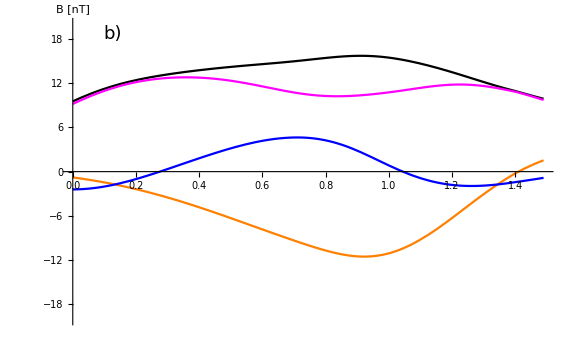

```mathematica
GraphicsRow[
{
Plot[{
Norm[{fxa[t+Min[tparamsa]],fya[t+Min[tparamsa]],fza[t+Min[tparamsa]]}],
fxa[t+Min[tparamsa]],fya[t+Min[tparamsa]],fza[t+Min[tparamsa]]
},{t,0,Max[tparamsa]-Min[tparamsa]},PlotRange->{- 20,20},PlotStyle->{Black,Magenta,Orange,Blue,{Dashed,Black},{Dashed,Magenta},{Dashed,Orange},{Dashed,Blue}},AxesLabel->{"","B [nT]"},PlotLegends->{"B_T","B_X","B_Y","B_Z"},Epilog->{Text[Style["a)",18],Scaled[{0.1,0.95}]]},ImageSize->Large,LabelStyle->{FontSize->14,FontColor->Black}],
Plot[{
Norm[{fxb[t+Min[tparamsb]],fyb[t+Min[tparamsb]],fzb[t+Min[tparamsb]]}],
fxb[t+Min[tparamsb]],fyb[t+Min[tparamsb]],fzb[t+Min[tparamsb]]
},{t,0,Max[tparamsb]-Min[tparamsb]},PlotRange->{-20,20},PlotStyle->{Black,Magenta,Orange,Blue,{Dashed,Black},{Dashed,Magenta},{Dashed,Orange},{Dashed,Blue}},AxesLabel->{"","B [nT]"},
Epilog->{Text[Style["b)",18],Scaled[{0.1,0.95}]]},ImageSize->Large,LabelStyle->{FontSize->14,FontColor->Black}]
},ImageSize->1000
]
```